## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* The Bates trap *)
currLa=0;
currZa=0;
currLb=0;
currZb=2.6;
currH = 2.6;

Bx1 = (-0.048)*40.625;
By1 = (0.43)*14.286;
Bz1 = (0.3003)*(-10.3675);

trapZHbB={currLa,currZa,currLb,currZb,currH,Bx1,By1,Bz1};
tableZHbB=convertTrapParametersToCALTable[trapZHbB,verbose->True];
(* *)

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=trapZHbB⟦3;;⟧
(* Where the x turn happens. *)
trapone={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
(*trapone=trapzero⟦1;;3⟧~Join~trapone⟦4;;6⟧*)
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
(*trapzero={0.11975890500000008,2.57197881,2.557757,-2.933909875000001,10.441794117420002,-2.4559802811975002}
trapone=trapZHbB⟦3;;7⟧~Join~{-3.1134}*)
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];
```

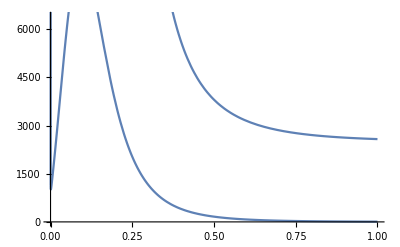

```mathematica
omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]
```

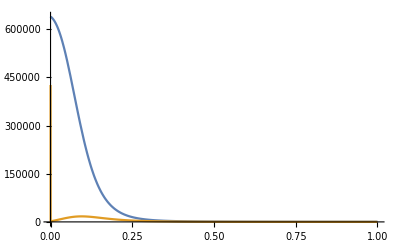

```mathematica
periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]
```

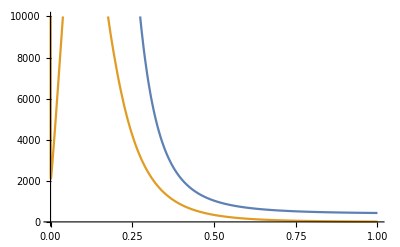

```mathematica
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]
```

21

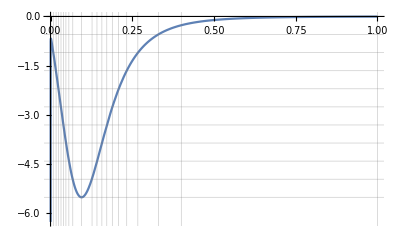

```mathematica
num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]
```

```mathematica
Length@Differences@times
```

20

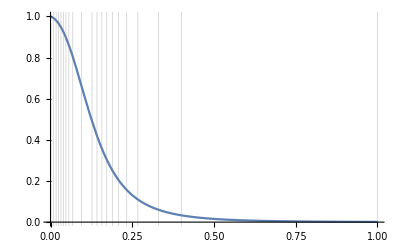

```mathematica
Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]
```

```mathematica
max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]
```

5.51458

```mathematica
dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];
```

```mathematica
(*InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv=InverseFunction@dCassShort*)
```

```mathematica
(*cassShortInv[-max]*)
```

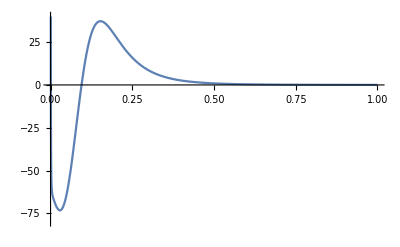

```mathematica
Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]
```

```mathematica
corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

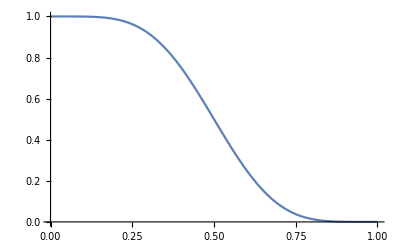

```mathematica
Plot[1-corgierSimp[t],{t,0,1}]
```

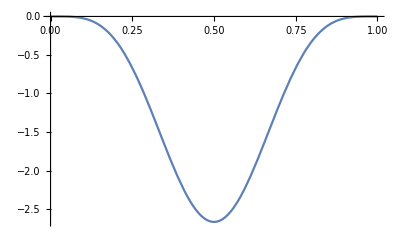

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]
```

```mathematica
InverseFunction[corgierSimp][8/3]
```

Root2.56Root[{-32-(8 Sin[2 π #1])/π+Sin[4 π #1]/π+12 #1&,2.56420663113429131513147635321}]2.5642066311342915

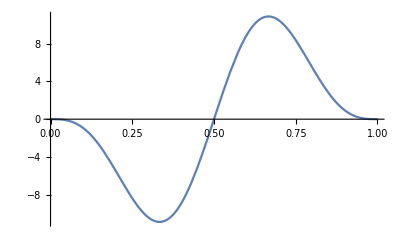

```mathematica
Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]
```

```mathematica
ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N
```

0.5-0.290925 ⅈ

```mathematica
trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;
```

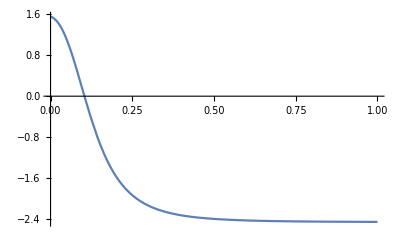

0.103674

tZero = 0.0518372

```mathematica
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]
```

```mathematica
Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]
```

{{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676},{0.05,1.09676}}

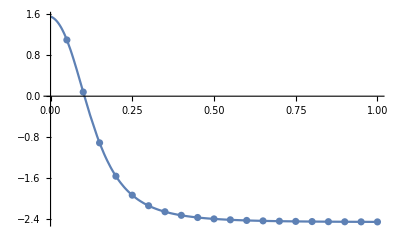

```mathematica
Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
(* Successful ramp with sharp tail "20200908T174440_trap1short.csv" *)
rampin1sguess={{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.02982,0.00749}}
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.15},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.02982,0.00749}}

```mathematica
rampin1sguess={Table[0.05,{k,20}],Table[0.05,{k,20}]}
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05},{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05}}

```mathematica
(*(* New as of 4 September 2020---an attempt to divy up the ramp based on its slope *)
Total@Differences@times
rampin1sguess={Differences@times,{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}*)
```

```mathematica
Table[Total@#[[1,1;;m]],{m,Length@#[[1]]}]&[rampin1sguess]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

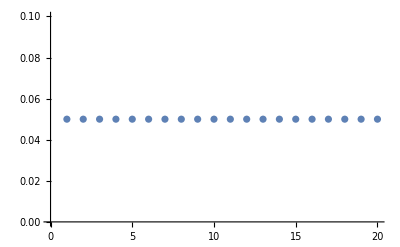

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

```mathematica
Length@rampin1sguess[[1]]
```

20

## Calculate ramp

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5,"CorgierSin"])//Timing
```

20

{0.05,-22.5875,0.149769,473.61,451.023,1.,0}

{0.025,-11.2697,0.149769,473.61,462.341,0.05,0}

{0.0125,-5.62611,0.149769,473.61,467.984,0.025,0}

{0.00625,-2.80843,0.149769,473.61,470.802,0.0125,0}

{0.00312,-1.39841,0.149769,473.61,472.212,0.00625,0}

{0.00156,-0.695919,0.149769,473.61,472.915,0.00312,0}

{0.00078,-0.344742,0.149769,473.61,473.266,0.00156,0}

{0.00039,-0.169171,0.149769,473.61,473.441,0.00078,0}

Completed point 1 of 19 in 87.8125 s (Total time: 1.46354 min).

{0.0526211,-23.676,0.149708,473.42,449.743,0.9998,0}

{0.02631,-11.7612,0.149708,473.42,461.658,0.0526211,0}

{0.01316,-5.82306,0.149708,473.42,467.596,0.02631,0}

{0.00658,-2.85629,0.149708,473.42,470.563,0.01316,0}

{0.00329,-1.37408,0.149708,473.42,472.045,0.00658,0}

{0.00164,-0.631018,0.149708,473.42,472.788,0.00329,0}

{0.00082,-0.261816,0.149708,473.42,473.158,0.00164,0}

Completed point 2 of 19 in 97.8125 s (Total time: 3.09375 min).

{0.0555217,-23.9624,0.149324,472.204,448.241,0.99939,0}

{0.02776,-11.3863,0.149324,472.204,460.817,0.0555217,0}

{0.01388,-5.11712,0.149324,472.204,467.087,0.02776,0}

{0.00694,-1.98756,0.149324,472.204,470.216,0.01388,0}

{0.00347,-0.42408,0.149324,472.204,471.78,0.00694,0}

{0.00174,0.355075,0.149324,472.204,472.559,0.00347,0}

Completed point 3 of 19 in 71.625 s (Total time: 4.2875 min).

{0.0586341,-22.4899,0.148037,468.133,445.643,0.99678,0}

{0.02932,-9.20188,0.148037,468.133,458.931,0.0586341,0}

{0.01466,-2.57667,0.148037,468.133,465.557,0.02932,0}

{0.00733,0.73042,0.148037,468.133,468.864,0.01466,0}

{0.011,-0.92491,0.148037,468.133,467.208,0.01466,0.00733}

Completed point 4 of 19 in 65.9844 s (Total time: 5.38724 min).

{0.0617263,-18.4924,0.145012,458.568,440.075,0.98762,0}

{0.03086,-4.48074,0.145012,458.568,454.087,0.0617263,0}

{0.01543,2.50278,0.145012,458.568,461.071,0.03086,0}

{0.02314,-0.984835,0.145012,458.568,457.583,0.03086,0.01543}

{0.01928,0.761714,0.145012,458.568,459.33,0.02314,0.01543}

Completed point 5 of 19 in 59.0313 s (Total time: 6.37109 min).

{0.0644273,-11.5426,0.139371,440.731,429.188,0.96641,0}

{0.03221,3.12007,0.139371,440.731,443.851,0.0644273,0}

{0.04832,-4.20592,0.139371,440.731,436.525,0.0644273,0.03221}

{0.04026,-0.539062,0.139371,440.731,440.192,0.04832,0.03221}

{0.03624,1.28864,0.139371,440.731,442.02,0.04026,0.03221}

{0.03825,0.374889,0.139371,440.731,441.106,0.04026,0.03624}

Completed point 6 of 19 in 91.8906 s (Total time: 7.9026 min).

{0.066225,-2.21145,0.130493,412.656,410.445,0.92715,0}

{0.03311,12.9105,0.130493,412.656,425.567,0.066225,0}

{0.04967,5.35237,0.130493,412.656,418.009,0.066225,0.03311}

{0.05795,1.5702,0.130493,412.656,414.227,0.066225,0.04967}

{0.06209,-0.321563,0.130493,412.656,412.335,0.066225,0.05795}

{0.06002,0.624372,0.130493,412.656,413.281,0.06209,0.05795}

{0.06106,0.149133,0.130493,412.656,412.805,0.06209,0.06002}

Completed point 7 of 19 in 93.8438 s (Total time: 9.46667 min).

{0.0665823,8.05642,0.118286,374.053,382.109,0.86557,0}

{0.46608,-167.925,0.118286,374.053,206.128,0.86557,0.0665823}

{0.26633,-82.4858,0.118286,374.053,291.567,0.46608,0.0665823}

{0.16646,-37.5247,0.118286,374.053,336.528,0.26633,0.0665823}

{0.11652,-14.7748,0.118286,374.053,359.278,0.16646,0.0665823}

{0.09155,-3.36482,0.118286,374.053,370.688,0.11652,0.0665823}

{0.07907,2.34301,0.118286,374.053,376.396,0.09155,0.0665823}

{0.08531,-0.511223,0.118286,374.053,373.542,0.09155,0.07907}

{0.08219,0.915822,0.118286,374.053,374.969,0.08531,0.07907}

{0.08375,0.202281,0.118286,374.053,374.255,0.08531,0.08219}

{0.08453,-0.154476,0.118286,374.053,373.898,0.08531,0.08375}

Completed point 8 of 19 in 179.422 s (Total time: 12.457 min).

{0.0651192,17.5996,0.103328,326.751,344.35,0.78143,0}

{0.42327,-137.112,0.103328,326.751,189.639,0.78143,0.0651192}

{0.24419,-62.5115,0.103328,326.751,264.239,0.42327,0.0651192}

{0.15465,-22.8813,0.103328,326.751,303.869,0.24419,0.0651192}

{0.10988,-2.71667,0.103328,326.751,324.034,0.15465,0.0651192}

{0.0875,7.42522,0.103328,326.751,334.176,0.10988,0.0651192}

{0.09869,2.34984,0.103328,326.751,329.101,0.10988,0.0875}

{0.10428,-0.18231,0.103328,326.751,326.568,0.10988,0.09869}

{0.10149,1.08122,0.103328,326.751,327.832,0.10428,0.09869}

{0.10288,0.451648,0.103328,326.751,327.202,0.10428,0.10149}

{0.10358,0.134651,0.103328,326.751,326.885,0.10428,0.10288}

Completed point 9 of 19 in 183.25 s (Total time: 15.5112 min).

{0.0615909,24.4817,0.0868112,274.521,299.003,0.6775,0}

{0.36955,-104.168,0.0868112,274.521,170.353,0.6775,0.0615909}

{0.21557,-42.5832,0.0868112,274.521,231.938,0.36955,0.0615909}

{0.13858,-9.54923,0.0868112,274.521,264.972,0.21557,0.0615909}

{0.10009,7.36066,0.0868112,274.521,281.882,0.13858,0.0615909}

{0.11934,-1.12491,0.0868112,274.521,273.396,0.13858,0.10009}

{0.10972,3.10889,0.0868112,274.521,277.63,0.11934,0.10009}

{0.11453,0.990253,0.0868112,274.521,275.512,0.11934,0.10972}

Completed point 10 of 19 in 138.094 s (Total time: 17.8128 min).

{0.056056,27.7695,0.0702948,222.292,250.061,0.56056,0}

{0.30831,-72.2402,0.0702948,222.292,150.052,0.56056,0.056056}

{0.18218,-24.6506,0.0702948,222.292,197.641,0.30831,0.056056}

{0.11912,1.06796,0.0702948,222.292,223.36,0.18218,0.056056}

{0.15065,-11.9276,0.0702948,222.292,210.364,0.18218,0.11912}

{0.13488,-5.46011,0.0702948,222.292,216.832,0.15065,0.11912}

{0.127,-2.20394,0.0702948,222.292,220.088,0.13488,0.11912}

{0.12306,-0.569926,0.0702948,222.292,221.722,0.127,0.11912}

{0.12109,0.248537,0.0702948,222.292,222.54,0.12306,0.11912}

{0.12208,-0.162893,0.0702948,222.292,222.129,0.12306,0.12109}

Completed point 11 of 19 in 120.703 s (Total time: 19.8245 min).

{0.0487756,27.3892,0.0553366,174.99,202.379,0.43898,0}

{0.24388,-44.4202,0.0553366,174.99,130.569,0.43898,0.0487756}

{0.14633,-10.3339,0.0553366,174.99,164.656,0.24388,0.0487756}

{0.09755,8.12708,0.0553366,174.99,183.117,0.14633,0.0487756}

{0.12194,-1.21066,0.0553366,174.99,173.779,0.14633,0.09755}

{0.10974,3.43416,0.0553366,174.99,178.424,0.12194,0.09755}

{0.11584,1.10515,0.0553366,174.99,176.095,0.12194,0.10974}

Completed point 12 of 19 in 80.4375 s (Total time: 21.1651 min).

{0.0400113,23.6553,0.0431291,136.386,160.042,0.32009,0}

{0.18005,-23.1784,0.0431291,136.386,113.208,0.32009,0.0400113}

{0.11003,-0.856832,0.0431291,136.386,135.529,0.18005,0.0400113}

{0.07502,11.1397,0.0431291,136.386,147.526,0.11003,0.0400113}

{0.09252,5.07611,0.0431291,136.386,141.462,0.11003,0.07502}

{0.10128,2.09094,0.0431291,136.386,138.477,0.11003,0.09252}

{0.10565,0.614465,0.0431291,136.386,137.001,0.11003,0.10128}

{0.10784,-0.122258,0.0431291,136.386,136.264,0.11003,0.10565}

{0.10674,0.247518,0.0431291,136.386,136.634,0.10784,0.10565}

{0.10729,0.0625623,0.0431291,136.386,136.449,0.10784,0.10674}

Completed point 13 of 19 in 170.984 s (Total time: 24.0148 min).

{0.0303614,18.0531,0.0342511,108.312,126.365,0.21253,0}

{0.12145,-9.33723,0.0342511,108.312,98.9743,0.21253,0.0303614}

{0.07591,3.86515,0.0342511,108.312,112.177,0.12145,0.0303614}

{0.09868,-2.85887,0.0342511,108.312,105.453,0.12145,0.07591}

{0.0873,0.470862,0.0342511,108.312,108.782,0.09868,0.07591}

{0.09299,-1.20169,0.0342511,108.312,107.11,0.09868,0.0873}

{0.09014,-0.365868,0.0342511,108.312,107.946,0.09299,0.0873}

{0.08872,0.0520181,0.0342511,108.312,108.364,0.09014,0.0873}

{0.08943,-0.157045,0.0342511,108.312,108.154,0.09014,0.08872}

{0.08908,-0.0540154,0.0342511,108.312,108.257,0.08943,0.08872}

Completed point 14 of 19 in 135.813 s (Total time: 26.2784 min).

{0.020605,11.8676,0.0286106,90.4747,102.342,0.12363,0}

{0.07212,-2.18442,0.0286106,90.4747,88.2903,0.12363,0.020605}

{0.04636,4.68895,0.0286106,90.4747,95.1636,0.07212,0.020605}

{0.05924,1.21445,0.0286106,90.4747,91.6891,0.07212,0.04636}

{0.06568,-0.494361,0.0286106,90.4747,89.9803,0.07212,0.05924}

{0.06246,0.357691,0.0286106,90.4747,90.8324,0.06568,0.05924}

{0.06407,-0.0689222,0.0286106,90.4747,90.4058,0.06568,0.06246}

{0.06326,0.145562,0.0286106,90.4747,90.6202,0.06407,0.06246}

{0.06366,0.0396069,0.0286106,90.4747,90.5143,0.06407,0.06326}

Completed point 15 of 19 in 118.563 s (Total time: 28.2544 min).

{0.011954,6.42006,0.0255857,80.9092,87.3292,0.05977,0}

{0.03586,0.346306,0.0255857,80.9092,81.2555,0.05977,0.011954}

{0.04781,-2.59734,0.0255857,80.9092,78.3118,0.05977,0.03586}

{0.04184,-1.13432,0.0255857,80.9092,79.7749,0.04781,0.03586}

{0.03885,-0.395913,0.0255857,80.9092,80.5133,0.04184,0.03586}

Completed point 16 of 19 in 63.1563 s (Total time: 29.307 min).

{0.005605,2.66169,0.0242986,76.8388,79.5005,0.02242,0}

{0.01401,0.610175,0.0242986,76.8388,77.449,0.02242,0.005605}

{0.01821,-0.403916,0.0242986,76.8388,76.4349,0.02242,0.01401}

{0.01611,0.102215,0.0242986,76.8388,76.941,0.01821,0.01401}

{0.01716,-0.151079,0.0242986,76.8388,76.6877,0.01821,0.01611}

{0.01664,-0.0256949,0.0242986,76.8388,76.8131,0.01716,0.01611}

{0.01638,0.0370389,0.0242986,76.8388,76.8758,0.01664,0.01611}

Completed point 17 of 19 in 87.0625 s (Total time: 30.7581 min).

{0.00197,0.746886,0.0239141,75.623,76.3699,0.00591,0}

{0.00394,0.273963,0.0239141,75.623,75.897,0.00591,0.00197}

{0.00492,0.0392962,0.0239141,75.623,75.6623,0.00591,0.00394}

{0.00541,-0.0778893,0.0239141,75.623,75.5451,0.00591,0.00492}

Completed point 18 of 19 in 44.1719 s (Total time: 31.4943 min).

{0.00037,0.0820129,0.0238537,75.4321,75.5141,0.00074,0}

{0.00055,0.0389995,0.0238537,75.4321,75.4711,0.00074,0.00037}

Completed point 19 of 19 in 30.6875 s (Total time: 32.0057 min).

{1925.95,{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05},{0.0002,0.00041,0.00261,0.00916,0.02121,0.03926,0.06158,0.08414,0.10393,0.11694,0.12158,0.11889,0.10756,0.0889,0.06386,0.03735,0.01651,0.00517,0.00064,0.0001}}}

```mathematica
FindTrapEndpoints[trapzero,trapone]
```

{473.617,75.4257}

```mathematica
startptsTest=Table[SingleTrapFrequency[trapzero,trapone,{{1},{1}},1,n],{n,2}];
```

```mathematica
startptsTest[[1,All]]
(ChipTrapFrequencies@@trapzero)[[4]]
```

{117.929,968.724,929.95}

{117.929,968.724,929.95}

```mathematica
GeometricMean@(startptsTest[[2,All]])
GeometricMean@((ChipTrapFrequencies@@trapone)[[4]])
```

75.4257

75.4257

```mathematica
GeometricMean[(ChipTrapFrequencies@@trapone)[[4]]]
```

75.4257

```mathematica
corgierSin[t_,ωi_,ωf_]:=Module[{tau=2*Pi*t},
ωi+((ωf-ωi)/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];
```

```mathematica
Plot[corgierSin[t,1,0],{t,0,1}]
```

-Graphics-

```mathematica
omegaMeanVF[trap0_,trap1_,fColl0_:0,fColl1_:1,deltaFColl_:0.1]:=Module[
{trapParametersVF=Table[trap0+(trap1-trap0)*fColl,{fColl,fColl0,fColl1,deltaFColl}],
omegasVF,omegaMeanVF},
omegasVF=Map[ChipTrapFrequencies@@#&,trapParametersVF];
Return[Map[GeometricMean[#[[4]]]&,omegasVF]];
];
```

```mathematica
fColl0=0.99;
fColl1=1;
deltaFColl=0.0005;
omegaMeans=omegaMeanVF[trapzero,trapone,fColl0,fColl1,deltaFColl]
```

{77.8348,77.7133,77.592,77.4708,77.3496,77.2286,77.1077,76.9869,76.8662,76.7456,76.6251,76.5047,76.3844,76.2642,76.1441,76.0241,75.9042,75.7844,75.6647,75.5451,75.4257}

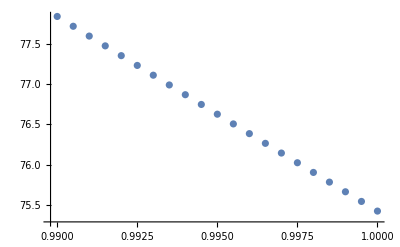

```mathematica
ListPlot[MapThread[{#1,#2}&,{Table[fColl,{fColl,fColl0,fColl1,deltaFColl}],omegaMeans}]]
```

```mathematica
Beep[];
```

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{-0.0498,-0.04959,-0.04739,-0.04084,-0.02879,-0.01074,0.01158,0.03414,0.05393,0.06694,0.07158,0.06889,0.05756,0.0389,0.01386,-0.01265,-0.03349,-0.04483,-0.04936,-0.0499}

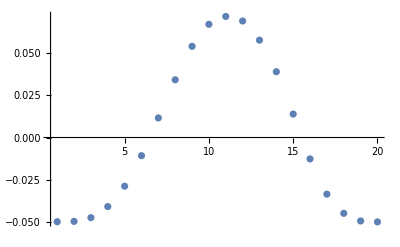

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

{507.,Null}

```mathematica
Position[pts1s⟦All,1,1⟧,Min@pts1s⟦All,1,1⟧]
```

{{88}}

```mathematica
pts1s⟦31⟧
```

{{0.0000714654,-0.0000209758,0.000144306},{111.052,895.493,860.364},8.69594}

```mathematica
Length@pts1s
```

101

```mathematica
trapParamVt=RampList[trapzero,trapone,rampin1s,points1s,nramps1short];
```

```mathematica
trapParamVt[[31]]
```

{0.3,{0.797266,2.41346,2.31878,-8.50014,34.7613,1.26299}}

### Plot calculated ramp’s parameters

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

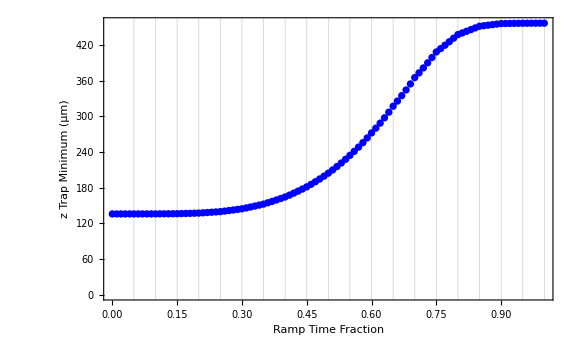
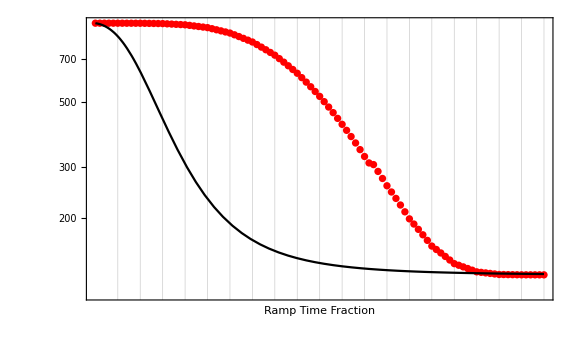

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{3.19789,4.77009}}

{24.4807,117.929}

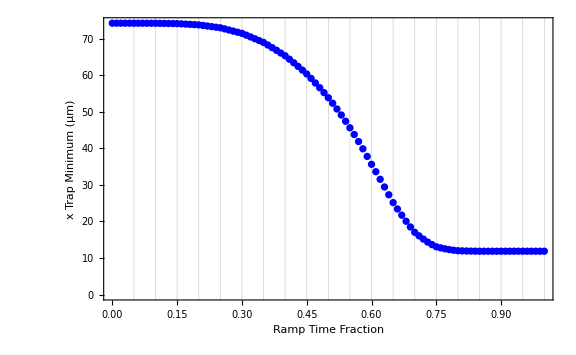
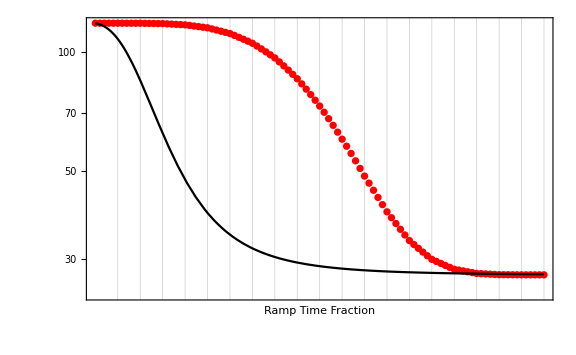

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{4.6421,6.87598}}

{103.762,968.724}

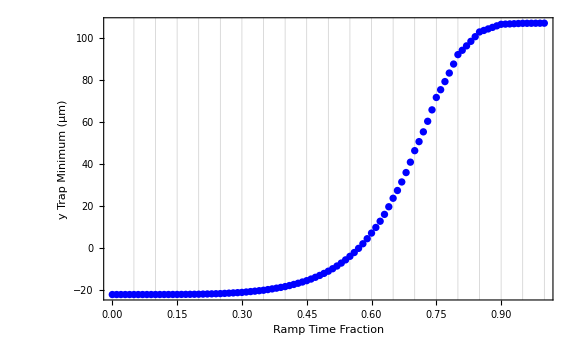
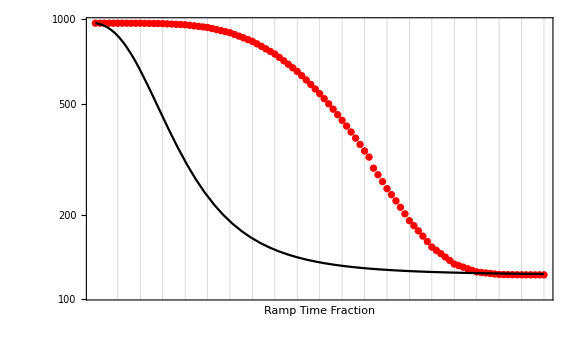

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{4.69813,6.83513}}

{109.742,929.95}

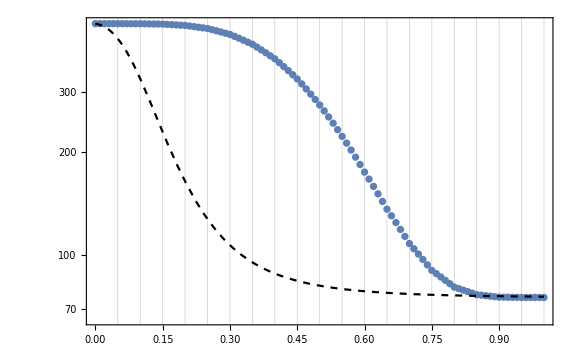

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

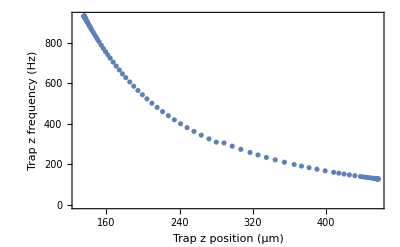

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

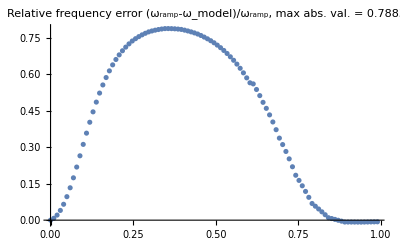

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {11.8576, 106.845, 456.854} μm
Frequency = {27.4397, 122.025, 128.153} Hz
Bmin = 5.60963 G

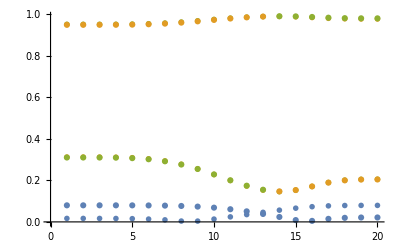

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

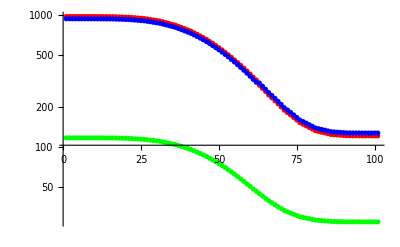

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05},{0.0002,0.00061,0.00322,0.01238,0.03359,0.07285,0.13443,0.21857,0.3225,0.43944,0.56102,0.67991,0.78747,0.87637,0.94023,0.97758,0.99409,0.99926,0.9999,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200909T165155

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20200909T165155_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20200909T165155_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.0342168,-0.734851,0.511551,0.00902742,0.00902742,0.242024,0.0789603}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.850471}, {0.02, 0.850442}, {0.03, 0.850412}, {0.04, 0.850383}, {0.05, 0.850354}, {0.06, 0.850294}, {0.07, 0.850234}, {0.08, 0.850174}, {0.09, 0.850114}, {0.1, 0.850054}, {0.11, 0.849673}, {0.12, 0.849291}, {0.13, 0.84891}, {0.14, 0.848528}, {0.15, 0.848147}, {0.16, 0.846808}, {0.17, 0.84547}, {0.18, 0.844131}, {0.19, 0.842792}, {0.2, 0.841453}, {0.21, 0.838354}, {0.22, 0.835254}, {0.23, 0.832154}, {0.24, 0.829054}, {0.25, 0.825954}, {0.26, 0.820217}, {0.27, 0.814479}, {0.28, 0.808741}, {0.29, 0.803003}, {0.3, 0.797266}, {0.31, 0.788266}, {0.32, 0.779266}, {0.33, 0.770266}, {0.34, 0.761266}, {0.35, 0.752266}, {0.36, 0.73997}, {0.37, 0.727673}, {0.38, 0.715376}, {0.39, 0.703079}, {0.4, 0.690782}, {0.41, 0.675593}, {0.42, 0.660404}, {0.43, 0.645214}, {0.44, 0.630025}, {0.45, 0.614836}, {0.46, 0.597745}, {0.47, 0.580655}, {0.48, 0.563564}, {0.49, 0.546474}, {0.5, 0.529383}, {0.51, 0.511614}, {0.52, 0.493846}, {0.53, 0.476077}, {0.54, 0.458308}, {0.55, 0.44054}, {0.56, 0.423164}, {0.57, 0.405789}, {0.58, 0.388413}, {0.59, 0.371037}, {0.6, 0.353662}, {0.61, 0.337942}, {0.62, 0.322222}, {0.63, 0.306503}, {0.64, 0.290783}, {0.65, 0.275063}, {0.66, 0.262071}, {0.67, 0.249078}, {0.68, 0.236086}, {0.69, 0.223093}, {0.7, 0.2101}, {0.71, 0.200767}, {0.72, 0.191434}, {0.73, 0.182101}, {0.74, 0.172768}, {0.75, 0.163435}, {0.76, 0.157977}, {0.77, 0.152518}, {0.78, 0.147059}, {0.79, 0.141601}, {0.8, 0.136142}, {0.81, 0.133729}, {0.82, 0.131316}, {0.83, 0.128903}, {0.84, 0.12649}, {0.85, 0.124078}, {0.86, 0.123322}, {0.87, 0.122566}, {0.88, 0.121811}, {0.89, 0.121055}, {0.9, 0.1203}, {0.91, 0.120206}, {0.92, 0.120113}, {0.93, 0.120019}, {0.94, 0.119926}, {0.95, 0.119832}, {0.96, 0.119817}, {0.97, 0.119803}, {0.98, 0.119788}, {0.99, 0.119774}, {1., 0.119759}}

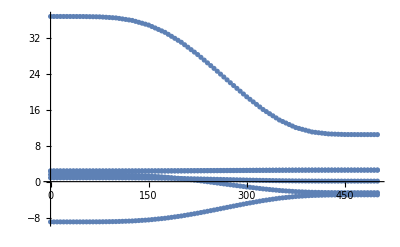

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

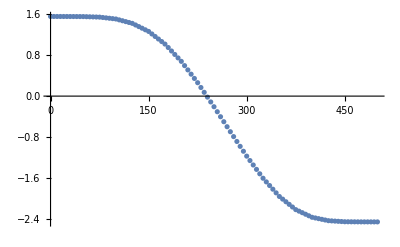

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05},{0.0002,0.00041,0.00261,0.00916,0.02121,0.03926,0.06158,0.08414,0.10393,0.11694,0.12158,0.11889,0.10756,0.0889,0.06386,0.03735,0.01651,0.00517,0.00064,0.0001}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.05,0.850354,2.40103,2.30005,-8.9363,36.6669,1.5544},{0.1,0.850054,2.4011,2.30016,-8.93384,36.6562,1.55275},{0.15,0.848147,2.40155,2.30083,-8.91817,36.5877,1.54228},{0.2,0.841453,2.40312,2.30319,-8.86318,36.3474,1.50554},{0.25,0.825954,2.40674,2.30866,-8.73584,35.7911,1.42046},{0.3,0.797266,2.41346,2.31878,-8.50014,34.7613,1.26299},{0.35,0.752266,2.42398,2.33465,-8.13044,33.146,1.01598},{0.4,0.690782,2.43837,2.35634,-7.6253,30.939,0.678476},{0.45,0.614836,2.45614,2.38313,-7.00134,28.2129,0.261594},{0.5,0.529383,2.47613,2.41327,-6.29928,25.1455,-0.207473},{0.55,0.44054,2.49692,2.44461,-5.56937,21.9564,-0.695152},{0.6,0.353662,2.51725,2.47525,-4.8556,18.8379,-1.17204},{0.65,0.275063,2.53564,2.50298,-4.20985,16.0165,-1.60348},{0.7,0.2101,2.55084,2.52589,-3.67613,13.6847,-1.96008},{0.75,0.163435,2.56176,2.54235,-3.29274,12.0096,-2.21623},{0.8,0.136142,2.56815,2.55198,-3.06851,11.0299,-2.36605},{0.85,0.124078,2.57097,2.55623,-2.96939,10.5968,-2.43227},{0.9,0.1203,2.57185,2.55757,-2.93835,10.4612,-2.45301},{0.95,0.119832,2.57196,2.55773,-2.93451,10.4444,-2.45558},{1.,0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598}

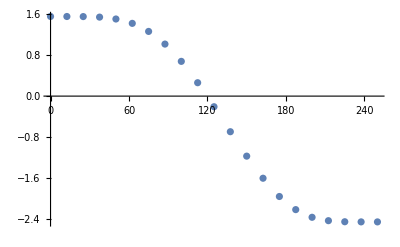

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15